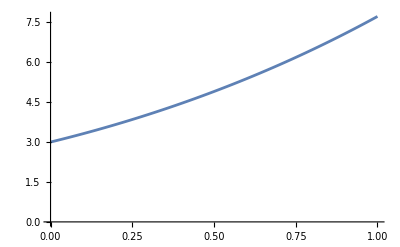

```mathematica
data = { {0, 3}, {0.02, 3.0606}, {0.04, 3.12241}, {0.06, 3.18544}, {0.08, 3.24969}, {0.1, 3.31517}, {0.12, 3.3819}, {0.14, 3.44987}, {0.16, 3.51911}, {0.18, 3.58962}, {0.2, 3.6614}, {0.22, 3.73448}, {0.24, 3.80885}, {0.26, 3.88453}, {0.28, 3.96153}, {0.3, 4.03986}, {0.32, 4.11953}, {0.34, 4.20055}, {0.36, 4.28293}, {0.38, 4.36668}, {0.4, 4.45182}, {0.42, 4.53836}, {0.44, 4.62631}, {0.46, 4.71567}, {0.48, 4.80647}, {0.5, 4.89872}, {0.52, 4.99243}, {0.54, 5.08761}, {0.56, 5.18427}, {0.58, 5.28244}, {0.6, 5.38212}, {0.62, 5.48333}, {0.64, 5.58608}, {0.66, 5.69039}, {0.68, 5.79628}, {0.7, 5.90375}, {0.72, 6.01283}, {0.74, 6.12354}, {0.76, 6.23588}, {0.78, 6.34987}, {0.8, 6.46554}, {0.82, 6.5829}, {0.84, 6.70197}, {0.86, 6.82276}, {0.88, 6.9453}, {0.9, 7.0696}, {0.92, 7.19569}, {0.94, 7.32358}, {0.96, 7.4533}, {0.98, 7.58486}, {1, 7.71828}};

ListPlot[data, Joined->True]
```

```mathematica
sol = DSolve[{y'[x]==y[x]-x^2, y[0]==3}, y[x], x];
```

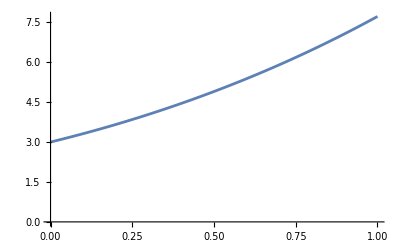

```mathematica
Plot[Evaluate[y[x]/.sol], {x, 0, 1}, AxesOrigin->{0,0}]
```

```mathematica
table=Table[{x,y[x]/. sol/. {val_}:>val},{x,0,1,0.02}];
Grid[table]
```

0. | 3.
0.02 | 3.0606
0.04 | 3.12241
0.06 | 3.18544
0.08 | 3.24969
0.1 | 3.31517
0.12 | 3.3819
0.14 | 3.44987
0.16 | 3.51911
0.18 | 3.58962
0.2 | 3.6614
0.22 | 3.73448
0.24 | 3.80885
0.26 | 3.88453
0.28 | 3.96153
0.3 | 4.03986
0.32 | 4.11953
0.34 | 4.20055
0.36 | 4.28293
0.38 | 4.36668
0.4 | 4.45182
0.42 | 4.53836
0.44 | 4.62631
0.46 | 4.71567
0.48 | 4.80647
0.5 | 4.89872
0.52 | 4.99243
0.54 | 5.08761
0.56 | 5.18427
0.58 | 5.28244
0.6 | 5.38212
0.62 | 5.48333
0.64 | 5.58608
0.66 | 5.69039
0.68 | 5.79628
0.7 | 5.90375
0.72 | 6.01283
0.74 | 6.12354
0.76 | 6.23588
0.78 | 6.34987
0.8 | 6.46554
0.82 | 6.5829
0.84 | 6.70197
0.86 | 6.82276
0.88 | 6.9453
0.9 | 7.0696
0.92 | 7.19569
0.94 | 7.32358
0.96 | 7.4533
0.98 | 7.58486
1. | 7.71828

```mathematica
data2 = { {0, 3}, {0.02, 3.0606}, {0.04, 3.1224}, {0.06, 3.18542}, {0.08, 3.24966}, {0.1, 3.31514}, {0.12, 3.38186}, {0.14, 3.44983}, {0.16, 3.51906}, {0.18, 3.58956}, {0.2, 3.66134}, {0.22, 3.73441}, {0.24, 3.80878}, {0.26, 3.88445}, {0.28, 3.96144}, {0.3, 4.03976}, {0.32, 4.11942}, {0.34, 4.20044}, {0.36, 4.28281}, {0.38, 4.36656}, {0.4, 4.45169}, {0.42, 4.53822}, {0.44, 4.62615}, {0.46, 4.71551}, {0.48, 4.8063}, {0.5, 4.89854}, {0.52, 4.99224}, {0.54, 5.0874}, {0.56, 5.18406}, {0.58, 5.28221}, {0.6, 5.38188}, {0.62, 5.48308}, {0.64, 5.58582}, {0.66, 5.69012}, {0.68, 5.796}, {0.7, 5.90346}, {0.72, 6.01253}, {0.74, 6.12322}, {0.76, 6.23554}, {0.78, 6.34953}, {0.8, 6.46518}, {0.82, 6.58253}, {0.84, 6.70158}, {0.86, 6.82236}, {0.88, 6.94488}, {0.9, 7.06917}, {0.92, 7.19524}, {0.94, 7.32311}, {0.96, 7.45281}, {0.98, 7.58436}, {1, 7.71776}};
```

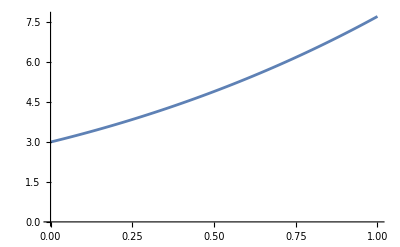

```mathematica
ListPlot[data2, Joined->True]
```